```mathematica
Get["LatticeLoops.wl"]
Information["LatticeLoops`*"]
```

```mathematica
R=20;
```

```mathematica
masses=Table[LoopMass[DiskSites[R]],{R,2,40,1}]
```

{0.96021,3.54308,7.07049,11.4767,19.2264,26.25,35.801,47.1498,58.4771,72.4884,85.6528,102.227,121.477,139.822,160.002,180.118,204.649,230.09,255.467,281.809,312.419,341.403,371.265,403.679,439.647,477.326,512.472,548.495,589.671,630.087,674.8,717.859,762.588,811.765,856.593,906.599,955.815,1011.06,1064.68}

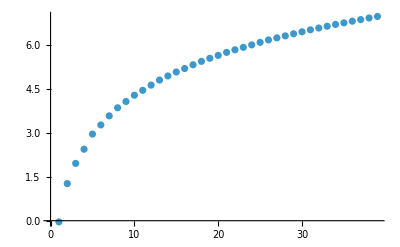

```mathematica
ListPlot[Log[masses]]
```

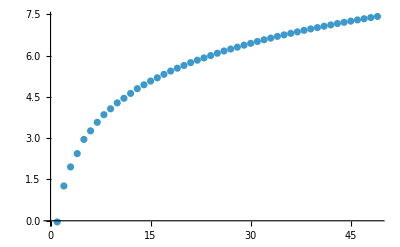

```mathematica
(*-Log[Det[1-P_D]] for D=DiskSites[R] (integer R,centered at the origin)*)diskLoopMass[R_Integer]:=Module[{ws,logdet=0.,Sinv,wP=-1,n,S,m},(*half-width of each row y:largest x with x^2+y^2<R^2*)ws=Floor[Sqrt[R^2-Range[-(R-1),R-1]^2-1]];
Do[n=2 w+1;
S=Normal[SparseArray[{Band[{1,1}]->1.,Band[{1,2}]->-0.25,Band[{2,1}]->-0.25},{n,n}]];
If[wP>=0,(*integrate out the previous rows:couple vertically adjacent sites*)m=Min[w,wP];
S[[w-m+1;;w+m+1,w-m+1;;w+m+1]]-=Sinv[[wP-m+1;;wP+m+1,wP-m+1;;wP+m+1]]/16];
logdet+=Log[Det[S]];
Sinv=Inverse[S];
wP=w,{w,ws}];
-logdet]

masses=Table[diskLoopMass[R],{R,2,50}];
ListPlot[Log[masses]]
```